# Neutral site proteomics report

#### Mathematica data analysis by Andrew Landels

## Experimental description

2 iTRAQ experiments were run as part of a single investigation into 5 neutral sites in the Synechocystis PCC6803 genome, denoted 5, 8, 10, 15 and 16. Controls in these experiments were the wild-type unmodified Synechocystis and a blank insert (at site 15). In all other cases GFP was inserted into the genome at the site of interest.

To link the two iTRAQ experiments together, the same WT Synechocystis samples were used in both cases. These experimental repeats are individually labelled in the experiment to differentiate them, this same differentiation is not done with any other samples.

The labels were assigned as follows:

label	iTRAQ a	iTRAQ b
113	aWT		bWT
114	aWT2		bWT2
115	a15-GFP	b5-GFP
116	a15-GFP	b5-GFP
117	a16-GFP	b8-GFP
118	a16-GFP	b8-GFP
119	a15-blank	b10-GFP
121	a15-blank	b10-GFP

Where a or b indicates the iTRAQ, the number indicates the site and the value following the hyphen indicates the treatment (GFP is shortened to G in the diagram labels).

## Standard proteome pipeline investigation

Initially, we analysed both iTRAQs individually with our proteome pipeline (Khoa et al. Proteomics. 2010 Sep;10(17):3130-41. doi: 10.1002/pmic.200900448) to generate a list of proteins that appeared to be significantly up or down regulated based on a P-value cut-off. Unfortunately, due to a loss of some experimental material from 1 of the iTRAQs (iTRAQ a) a direct comparison using the standard pipeline was difficult to acheive.

We produced a series of initial figures assessing the iTRAQs individually for relatedness and sent a list of proteins from signifiQuant which passed the statistical stringency test for being up or down regulated.

To generate a more informative analysis, we decided to investigate the effects of the combination of both iTRAQs in more detail, particularly from a clustering point of view. The first step was to work forward from the data that we had gathered from our proteomics pipeline. 

(1)	iTRAQ a 	464 proteins (with 2 or more peptides)
(2)	iTRAQ b 	631 proteins (with 2 or more peptides)

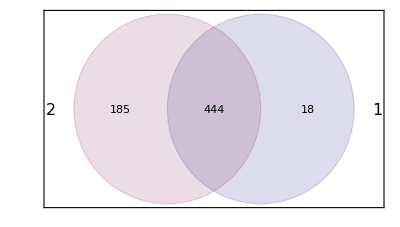

We found an intersection of 444 proteins that had been successfully quantified by the standard method, so decided to solely use these proteins to assess clustering with PCA.

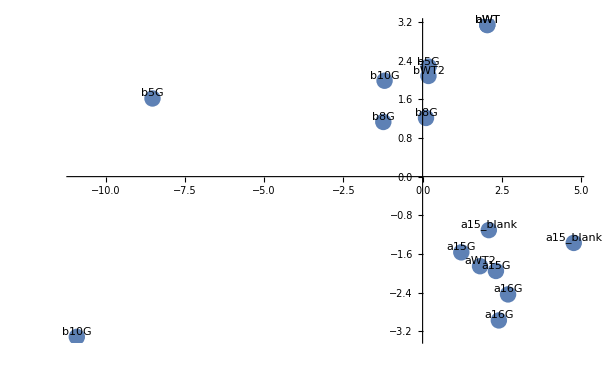

The values in this investigation were all generated relative to tag 113 (WT), which forms a joining point between the two datasets, however with the exception of the linking tag the two iTRAQs cluster separately. This is particularly notable for WT2 and is likely due to either the additional information present in iTRAQ b, or the manner in which the standard pipeline handles 0-intensity values.

As a result, it is difficult to draw clear conclusions about the features of the sites in general by meta-analysis of the terminal data alone.

## Manually normalising the data

The first step was to look at the raw peptide information. The number of peptide spectral matches (PSMs) was compared.

iTRAQ		PSMs		Unique Sequences	Proteins
a		7999		1923 				540
b		14814		3306 				722

In total, 749 unique proteins had been identified with at least 1 PSM

We assessed both Channel sum - equalising the sum total intensity for each label - and median correction as normalisation methods for this data. Median correction was used as it produced a better ranking effect.

As certain proteins (notably GFP) were either below the level of detection or not present in all samples, a value α was added to all the label intensities. This has two benefits, firstly as we’re interested in ratio data it removes 0s from the analysis which removes the infinite value (divide by 0) issue from the analysis. Secondly, as α is a fixed value it masks low-intensity labels which can contribute to abnormally large ratio readings. This is shown below for iTRAQ a, but the graph for iTRAQ b is almost identical (with the exception of the x-axis being almost double the range).

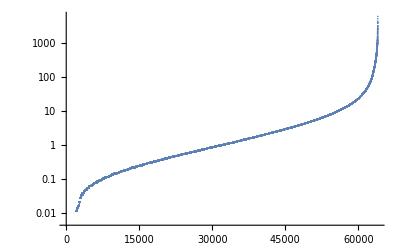

Prior to α addition, x-axis = ranked PSMs by reporter intensity, y-axis = intensity.

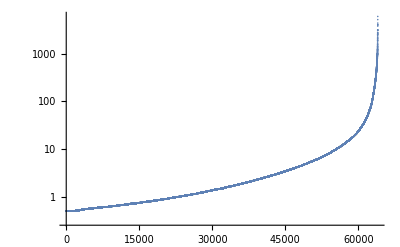

Following α addition. α is set as 0.5, which removes the inaccurate low-intensity readings whilst not affecting the high-intensity readings.

The next step was to select only high-quality proteins for comparative analysis. As a result, the datasets were filtered by peptides twice - only proteins that had both 3 or more peptides for quantification AND at least 2 unique sequence matches were retained. A total of 552 conidently identified and quantified unique proteins were found in the entire investigation, of which 365 overlapped between the two experiments.

iTRAQ		PSMs		Unique Sequences	Proteins	Intersecting Proteins
a		7656		1719 				371		365
b		13327		3090 				546		365

The intensity values were converted to natural log form and the geometric mean was calculated for each of the common proteins. The final step in normalisation was to generate ratios. To avoid having a single label generating all the ratios and therefore having all values on that label collapsed down to 1, all labels were divided by the mean of both the WT samples in each iTRAQ.

## Cluster Analysis

The first step in assessing the normalised data is to quickly look at all the values to check consistency with a heatmap.

At a glance (not shown), the WT labels show very similar patterning which is a good sign. On close examination there is a checker - board type effect, indicating that the experimental samples are varying in similar directions rather than clustering by experimental replicate.

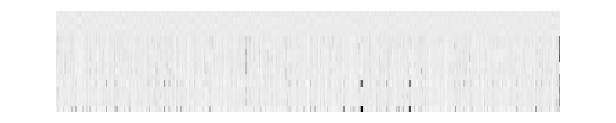

The test conditions also look like they have the correct patterning. The telltale sign of this is the GFP intensities (right - most column) which are visible for all samples that have GFP, but not for the WT (top 4 rows) or the blank (middle rows) controls. A second, larger version of this heatmap is provided as an appendix at the end of this report.

Over-interpretation of a heatmap can be misleading, however there do seem to be certain proteins in b5-GFP and b10-GFP that show similar patterning. This is clearer when using cluster tools such as a dendrogram or heatmap.

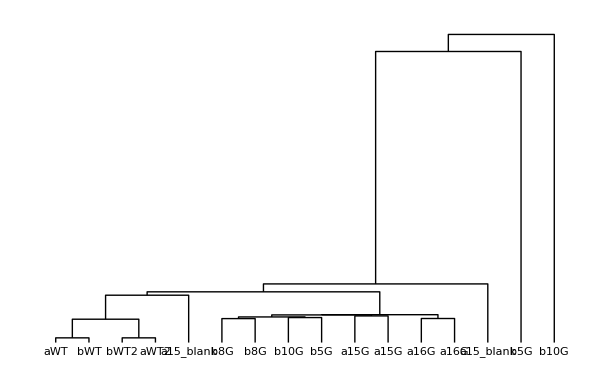

This dendrogram shows a clear relatedness between matching wild-type Synechocystis samples from the different iTRAQ experiments. It nicely demonstrates the amount of experimental variation (a vs b) as well as the experimental variation (WT vs WT2).

The GFP mutants all cluster clearly together away from the WT controls, although the blanks don’t appear to be clearly separated in this graphic. The amount of experimental variation between paried samples for sites 8, 15 and 16 match the expected experimental variation (based on the WT controls). The variation beyond experimental variation for these samples appears to be minimal. 

Notably, b5-GFP and b10-GFP have suppressed the diagram by being significantly different to all the other samples, reflecting the observation made earlier on the heatmap.

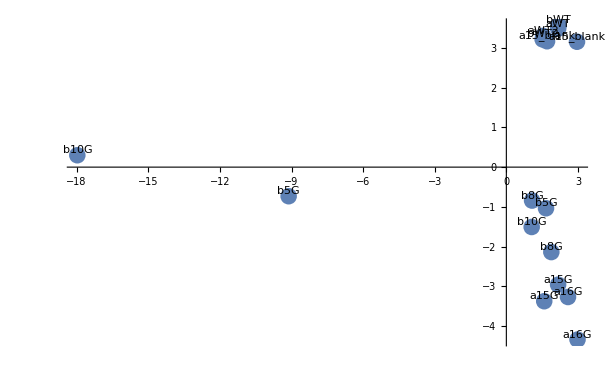

The pca plot clearly shows 3 clusters. For a simple interpretation of the axes, the y-axis relates to the amount of GFP detected, where lower values on the axis indicates an increased amount of GFP. The x-axis (responsible for the majority of the data variation) appears to be related to other background effects within the cell.

The top-right quadrant contains the control samples including the blank insertion control, the experimental-replicate clustering is clearer on the dendrogram as the samples are too crowded on the PCA, however it is interesting to note that the blank clusters closely to the WT, albeit with slightly more variation between the two experimental repeats than the unmodified cells. 

The lower-right quadrant contains most of the GFP insertion mutants. The 15-blank cells show the same amount of x-axis spread-separation between the biological replicates as amongst all the clustered GFP-insertion mutants, suggesting that there are no major side-effects proteomically as a result of gene insertion into 3 of the neutral sites - 8, 15 and 16..

The left-half of the plot contains the final two samples, b10-GFP and b5-GFP. These show notable changes in the background variation axis, although as only an individual repeat has shown this effect in both cases it is difficult to assess statistically significant site-specific effects from the data we have available.

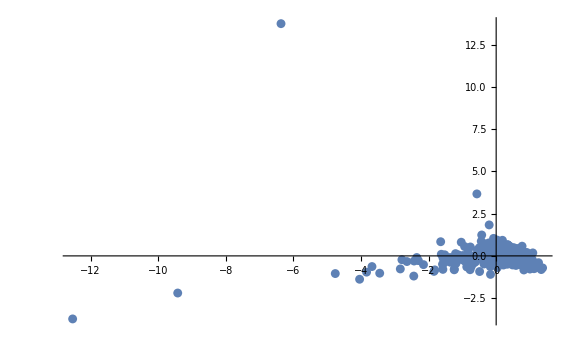

PCA plot of proteins. A version with annotation is in the appendix, however the labels are cluttered and difficult to read.

The protein PCA shows a relatively small number of proteins that stand out from the rest of the proteins identified in the experiment, however these don’t shed much light on pathway-level changes withing the cell. 

Here we’ve highlighted a couple of directions of change on the PCA, the trend towards the bottom left corner is purely centered around photosystems, energy and carbon fixation. The 3 proteins pushing away from the bulk of the proteins at a perpendicular angle towards the middle top are mostly uncharacterised and don’t show any specific trend in function.

(top center)
P42212 = GFP 

Direction 1 (Origin towards bot left, starting on the left)
P29254 = PS1
P29256 = PS1
m1m7g3 = phycobili prot 
m1m7t6 = ribulose bisphosphate carboxylase
m1ml90 = fructose bisphosphate aldolase
m1lgt6 = atp synthase
m1mdr0 = uncharacterised aldehyde lyase
m1lzc3 = phycobili prot

Direction 2 (middle right, starting from the top)
m1mf82 = uncharacterised (hydrolase GO)
m1lhp6 = quinone oxireductase
F7URK1 = uncharacterised

## Relative GFP levels

The table below shows the relative amounts of GFP that have been detected. It is important to note that these values have been calculated relative to a given α value and so values from non-GFP producing strains can be considered as the noise level. As a result, the variation between iTRAQ a and iTRAQ b make cross-iTRAQ investigation of these values impractical.

Each table contains two rows, the first is the Log of protein intensity, the second is the predicted ratio-linear values.

aWT | aWT2 | a15G | a15G | a16G | a16G | a15_blank | a15_blank
1.00393 | 0.996067 | 7.28006 | 6.80283 | 6.77149 | 8.11185 | 0.556368 | 0.866531
2.72899 | 2.70761 | 1451.07 | 900.393 | 872.612 | 3333.73 | 1.74433 | 2.37864

bWT | bWT2 | b5G | b5G | b8G | b8G | b10G | b10G
0.98286 | 1.01714 | 5.01068 | 3.9141 | 5.99852 | 4.63505 | 5.25372 | 2.30489
2.67209 | 2.76528 | 150.007 | 50.104 | 402.832 | 103.033 | 191.276 | 10.0231

Sample a15-GFP seems to have the most consistent GFP production levels. Generally speaking, the protein production in neutral sites tends to vary by up to about a 4-fold amount between replicates. It is important to note that the outlying b10-GFP has much lower GFP intensity than its experimental counterpart, a 20-fold reduction with measured levels approaching the noise level. 

b5-GFP production seems to be about half that of b8-GFP. This might be an indicator of genetic interference with protein production in these sites. 

To generate more accurate data on these values, it might be worthwhile running a targeted proteomics experiment to get directly relatable spectral counts on all these proteins, coupled with some other form of measurement such as transcript analysis or fluorescence intensity.

## Further work

These are things that I intended to do with this report, but had so much trouble re-working the data into a compatible form that I decided to send on what I had now just so you could see that we’re making progress. Apologies again for the delay with this - I’m still learning a lot on the way! :-)

* Run signifiQuant with b10G and b5G vs WT to look for specific proteins that seem to be coming up in the heatmap.

* Re-work the α value to be relatively peptide specific to make the GFP values more stable. (I’ve done this on a previous analysis and I’m still undecided what the best way to go forward with it is)

* Generate a protein-labelled dendrogram-heatmap in the R, to look more closely at the protein-specific clusters in the data rather than just the label clustering effects. This might highlight protein families of interest that whilst not appearing on the signifiQuant analysis might make sense in GO terms or on a KEGG map.

## Appendix - heatmap

The columns are (from left to right)
4x WT, 2x 15-GFP, 2x 16-GFP, 2x 15-blank, 2x 5-GFP, 2x 8-GFP, 2x 10-GFP

The outliers are the far-right column and 5th from the right.
GFP is the very bottom row.

There are a couple more obvious effects from this image, but I’ll need to work on it a bit more to find out which proteins they are. Hopefully a more comprehensive dendrogram will help, regrettably Mathematica can’t produce heatmaps with labels very easily.

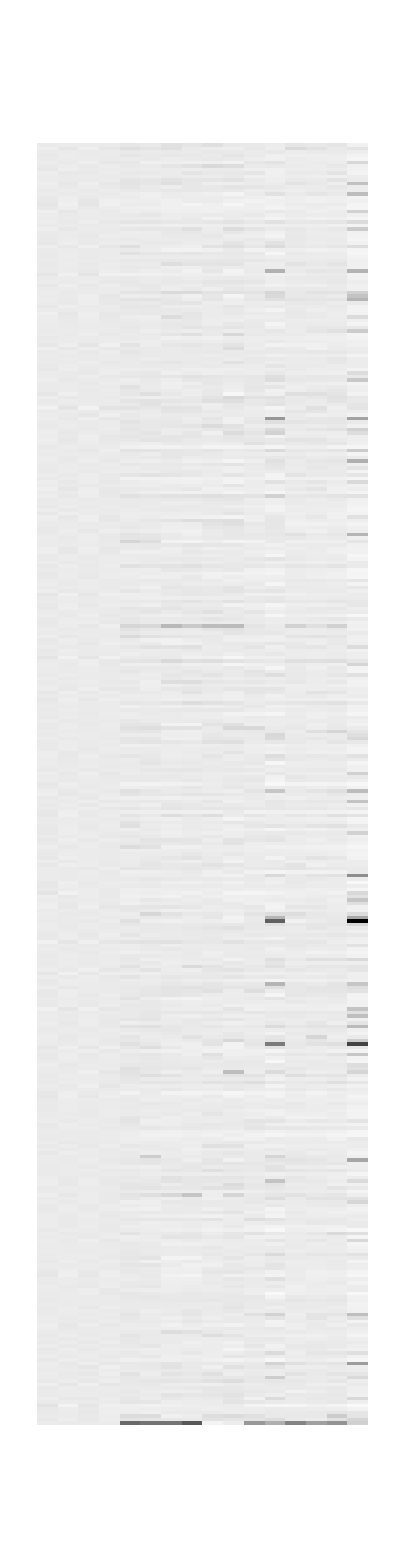

Annotated Protein PCA (difficult to read)